-0.151304

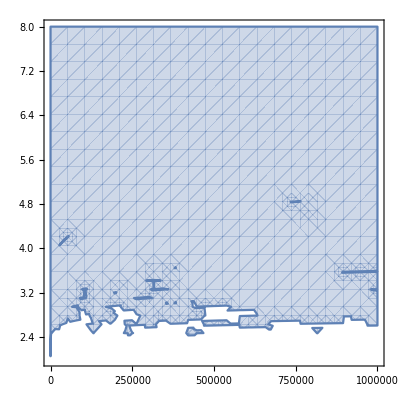

```mathematica
Remove[f,v,a];
l23=Log2[3];
(*f[v_,a_]:=IntegerPart[l23*IntegerPart[(Log2[(3*v-v*2^a+1)/(4-2^a)])/(a-l23)]+Log2[v]]+1-a*IntegerPart[(Log2[(3*v-v*2^a+1)/(4-2^a)])/(a-l23)];*)
f[v_,a_]:=(Log2[v]+0.0000001)/(a-l23)-IntegerPart[(Log2[-3*v+2^a*v-1]-Log2[-4+2^a])/(a-l23)];
Print[f[310,3]];
RegionPlot[0≤f[v,a],{v,1,1000000},{a,2,8}]
(*Plot3D[f[v,a],{v,1,200},{a,1,10}]*)
```